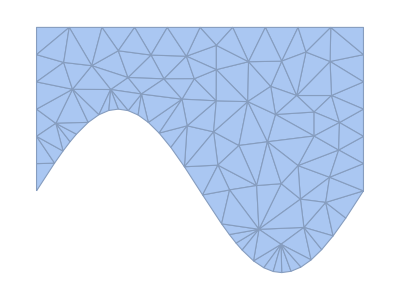

/home/san/Code/Laplace_eq/meshes/mesh1.stl

/home/san/Code/Laplace_eq/meshes/mesh1.obj

```mathematica
model =DiscretizeRegion[ImplicitRegion[y>= Sin[1/2 π*x] && y <= 2 && 0<=x<=4, {{x,0,4},{y,-1,2}}], MaxCellMeasure->0.1]
Export["/home/san/Code/Laplace_eq/meshes/mesh1.stl", model,  {"STL", "BinaryFormat" -> False}]
```

```mathematica
Ω=ImplicitRegion[y>= Sin[x] && y <= 2 && 0<=x<=2π, {{x,0,2π},{y,-1,2}}];
RegionPlot[Ω,AspectRatio->Automatic]
```

-Graphics-

```mathematica
ufun=
NDSolveValue[
{-Laplacian[u[x,y],{x,y}]==0,
PeriodicBoundaryCondition[u[x,y],x==0 ,TranslationTransform[{2π,0}]],
DirichletCondition[u[x,y]==10,y==2 && 0<x<2π],DirichletCondition[u[x,y]==100,y -Sin[x]==0 && 0<x<2π]},
u,{x,y}∈Ω,Method->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->0.0001,"MeshElementType"->TriangleElement}}]
```

InterpolatingFunction[{{0., 6.28319}, {-1., 2.}}, <>]

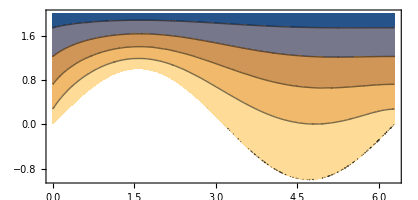

```mathematica
ContourPlot[ufun[x,y],{x,y}∈Ω,AspectRatio->Automatic]
```

```mathematica
reg = MeshRegion[{{0.,0.},{0.22055117451721412,0.33955239167528295},{0.32412393069948864,0.4874201143956197},{0.4104847072310811,0.6010289122140435},{0.4881128059494951,0.6937809302033444},{0.6320772802621745,0.8375943615288411},{0.7625718281066655,0.9312560510634783},{0.8848733016097592,0.9836928538590948},{1.000000000000005,1.},{1.1207883485437105,0.982054456792746},{1.2426753444628058,0.9282212659225965},{1.3680453072991685,0.8374891518337156},{1.5000284665069992,0.7070751621400859},{1.643661767205692,0.5309614763164495},{1.8094003453508183,0.29494048985621424},{2.031763994313858,-0.049874066102280075},{2.2640781032737243,-0.40301871843627207},{2.3590291919467576,-0.5345386215772783},{2.4412011973914924,-0.6388766866952208},{2.515937865915456,-0.72458586923369},{2.654668064546828,-0.8564484701133004},{2.7806792446429136,-0.9412416514540224},{2.8964596449755358,-0.9868031124580505},{2.999999980154588,-0.9999999999999996},{3.114326342360129,-0.9839181913742655},{3.235656714482532,-0.9322663272756924},{3.359892702133432,-0.8444182234155081},{3.489592594181542,-0.7185715011647854},{3.628532838164962,-0.5509475703249581},{3.784040275696842,-0.3327598856393173},{4.,-2.067303301293235*^-14},{0.,0.3333333333333333},{0.,0.6666666666666666},{0.,1.},{0.,1.3333333333333333},{0.,1.6666666666666665},{0.,2.},{4.,0.33333333333331616},{4.,0.666666666666653},{4.,0.9999999999999898},{4.,1.3333333333333266},{4.,1.6666666666666634},{4.,2.},{0.4,2.},{0.8,2.},{1.2000000000000002,2.},{1.6,2.},{2.,2.},{2.4000000000000004,2.},{2.8000000000000003,2.},{3.2,2.},{3.6,2.},{2.9914630533496593,-0.6542015571774351},{0.23596108447693673,0.8259562695263363},{1.1191840963669915,1.3867320292415344},{2.7212453422623364,-0.4701228939022447},{0.9072418849636632,1.2403176895837387},{1.2832717630558201,1.1850405513973654},{0.4397851168467894,1.2432431242141397},{1.7795811677502598,1.1219841018437895},{3.2287906478209,-0.10153128785617116},{2.1664539387543593,0.7218734824310233},{3.1833333333333247,1.166666666666658},{3.585769915707288,0.16666666666664776},{3.608673469387751,1.166666666666658},{1.4000000000000001,1.6616852701615663},{1.,1.7143969117188835},{2.2,1.483116470993668},{2.2191208526505064,0.3150545243358832},{3.0000000000000004,1.5871666666666644},{2.2,1.7802516719823194},{2.8253265143654653,0.600352722273441},{2.476351138946355,0.5551742572994082},{2.693169042759511,0.06506632992236083},{2.584211549877488,1.092417516661109},{2.361836039984251,0.011224113994152296},{3.5379671862840265,-0.14138037660767527},{3.396003401360538,0.671275280600345},{3.696712418612736,0.49999999999998457},{1.5589496309701698,1.3701437103194407},{1.8332923690056149,1.647386668507777},{1.9300969014261935,1.3720437752658974},{2.199118296248055,1.1017946859609111},{0.6753285486425609,1.531807858018539},{0.33213148251051827,1.571530861100007},{2.8653440034763946,1.2782424972218422},{2.5941304175798936,1.5802704213586374},{2.9233684647999296,0.9346911190142604},{3.3960034013605376,0.9646202916342037},{3.1993471883089293,0.30933267668131087},{2.994063846584715,0.08813462346534628},{3.271444144087613,-0.44713927350720994},{1.8430386908576064,0.7962503416618805},{3.591555811722523,1.583200307400362},{3.2965368151008354,1.698369696627236},{3.7065717945219983,0.8360029044767063}},{Polygon[{{1,2,32},{46,66,47},{32,2,33},{69,73,62},{3,4,54},{3,33,2},{35,85,36},{4,5,54},{7,57,59},{39,40,96},{55,67,84},{12,13,60},{62,93,15},{92,56,53},{34,33,54},{10,11,58},{58,12,60},{45,67,46},{92,53,27},{57,58,55},{80,81,66},{54,33,3},{57,55,84},{59,54,6},{34,54,59},{6,7,59},{34,59,35},{94,41,42},{36,44,37},{59,85,35},{66,55,80},{58,80,55},{57,7,8},{65,63,89},{92,29,77},{77,29,30},{58,57,10},{57,9,10},{66,67,55},{84,59,57},{73,75,62},{12,58,11},{46,67,66},{82,60,83},{71,81,68},{8,9,57},{6,54,5},{44,84,45},{93,62,83},{65,89,96},{22,53,21},{69,15,16},{90,61,64},{56,21,53},{20,56,19},{66,81,47},{61,77,64},{56,18,19},{53,22,23},{89,78,96},{24,25,53},{89,88,78},{31,77,30},{26,53,25},{27,28,92},{74,69,76},{56,20,21},{70,86,63},{17,76,16},{27,53,26},{77,61,92},{23,24,53},{50,70,51},{64,77,31},{48,71,49},{56,74,76},{40,41,65},{62,15,69},{50,49,87},{68,75,87},{94,65,41},{94,63,65},{56,17,18},{82,83,68},{64,31,38},{61,91,56},{73,72,75},{73,74,72},{52,94,42},{64,79,90},{42,43,52},{87,71,68},{69,74,73},{95,51,70},{16,76,69},{86,87,75},{56,91,74},{81,71,48},{88,72,78},{93,13,14},{79,38,39},{56,76,17},{90,79,78},{64,38,79},{58,60,80},{80,82,81},{47,81,48},{80,60,82},{60,93,83},{68,81,82},{62,75,83},{75,68,83},{45,84,67},{85,44,36},{59,84,85},{44,85,84},{86,70,87},{88,75,72},{50,87,70},{71,87,49},{63,86,88},{75,88,86},{88,89,63},{96,78,79},{78,72,90},{91,72,74},{61,90,91},{72,91,90},{29,92,28},{56,92,61},{13,93,60},{15,93,14},{95,52,51},{94,95,63},{63,95,70},{52,95,94},{39,96,79},{65,96,40}}]},Method->{"PropagateMarkers"->False}];
```

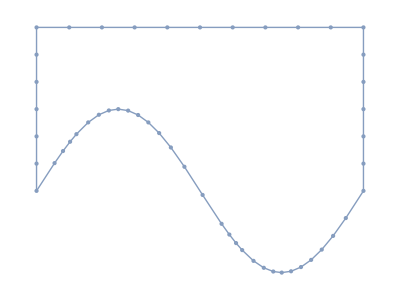

/home/san/Code/Laplace_eq/meshes/mesh_bound.csv

```mathematica
regBound=RegionBoundary[reg]
Export["/home/san/Code/Laplace_eq/meshes/mesh_bound.csv", regBound] (*,  {"STL", "BinaryFormat" -> False}]*)
```

```mathematica
plb = MeshRegion[{{0.,0.},{0.22055117451721412,0.33955239167528295},{0.32412393069948864,0.4874201143956197},{0.4104847072310811,0.6010289122140435},{0.4881128059494951,0.6937809302033444},{0.6320772802621745,0.8375943615288411},{0.7625718281066655,0.9312560510634783},{0.8848733016097592,0.9836928538590948},{1.000000000000005,1.},{1.1207883485437105,0.982054456792746},{1.2426753444628058,0.9282212659225965},{1.3680453072991685,0.8374891518337156},{1.5000284665069992,0.7070751621400859},{1.643661767205692,0.5309614763164495},{1.8094003453508183,0.29494048985621424},{2.031763994313858,-0.049874066102280075},{2.2640781032737243,-0.40301871843627207},{2.3590291919467576,-0.5345386215772783},{2.4412011973914924,-0.6388766866952208},{2.515937865915456,-0.72458586923369},{2.654668064546828,-0.8564484701133004},{2.7806792446429136,-0.9412416514540224},{2.8964596449755358,-0.9868031124580505},{2.999999980154588,-0.9999999999999996},{3.114326342360129,-0.9839181913742655},{3.235656714482532,-0.9322663272756924},{3.359892702133432,-0.8444182234155081},{3.489592594181542,-0.7185715011647854},{3.628532838164962,-0.5509475703249581},{3.784040275696842,-0.3327598856393173},{4.,-2.067303301293235*^-14},{0.,0.3333333333333333},{0.,0.6666666666666666},{0.,1.},{0.,1.3333333333333333},{0.,1.6666666666666665},{0.,2.},{4.,0.33333333333331616},{4.,0.666666666666653},{4.,0.9999999999999898},{4.,1.3333333333333266},{4.,1.6666666666666634},{4.,2.},{0.4,2.},{0.8,2.},{1.2000000000000002,2.},{1.6,2.},{2.,2.},{2.4000000000000004,2.},{2.8000000000000003,2.},{3.2,2.},{3.6,2.}},{Line[{{1,2},{32,1},{47,46},{33,32},{3,4},{2,3},{36,35},{4,5},{39,40},{12,13},{34,33},{10,11},{46,45},{6,7},{35,34},{41,42},{44,37},{37,36},{7,8},{29,30},{9,10},{11,12},{8,9},{5,6},{45,44},{21,22},{15,16},{19,20},{18,19},{22,23},{24,25},{30,31},{25,26},{27,28},{20,21},{16,17},{26,27},{23,24},{51,50},{49,48},{40,41},{50,49},{17,18},{31,38},{42,43},{43,52},{13,14},{38,39},{48,47},{28,29},{14,15},{52,51}}]}, MeshCellStyle->Red];
```

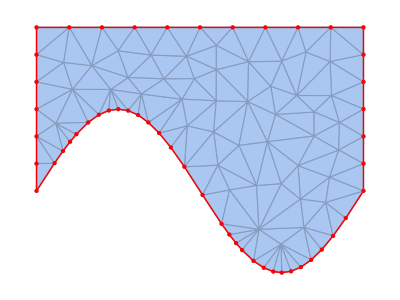

```mathematica
Show[reg, plb]
```

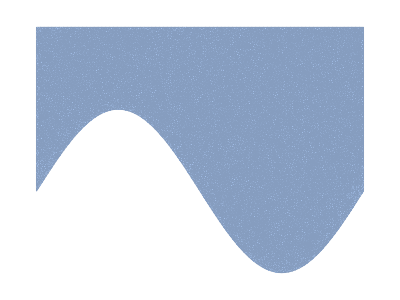

```mathematica
DiscretizeRegion[ImplicitRegion[y>= Sin[1/2 π*x] && y <= 2 && 0<=x<=4, {{x,0,4},{y,-1,2}}], MaxCellMeasure->0.001]
```

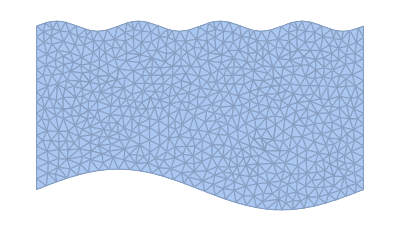

```mathematica
DiscretizeRegion[ImplicitRegion[y>= 1/4 Sin[1/2 π*x] && y <=2+ 1/16 Sin[2*π*x] && 0<=x<=4, {{x,0,4},{y,-5,5}}], MaxCellMeasure->0.01]
```

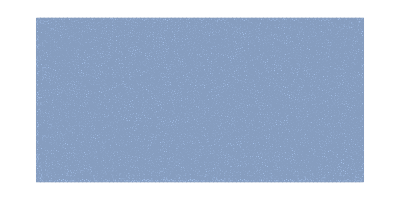

```mathematica
DiscretizeRegion[ImplicitRegion[y>=0 && y <= 2 && 0<=x<=4, {{x,0,4},{y,0,2}}], MaxCellMeasure->0.001]
```

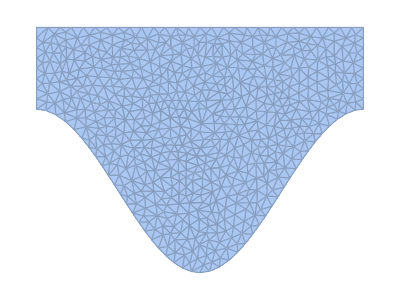

```mathematica
DiscretizeRegion[ImplicitRegion[y>= Sin[1/2 π*x] && y <= 2 && 1<=x<=5, {{x,0,5},{y,-1,2}}], MaxCellMeasure->0.01]
```

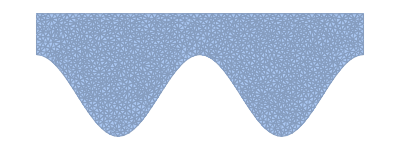

```mathematica
DiscretizeRegion[ImplicitRegion[y>= Sin[1/2 π*x] && y <= 2 && 1<=x<=9, {{x,0,10},{y,-1,2}}], MaxCellMeasure->0.01]
```

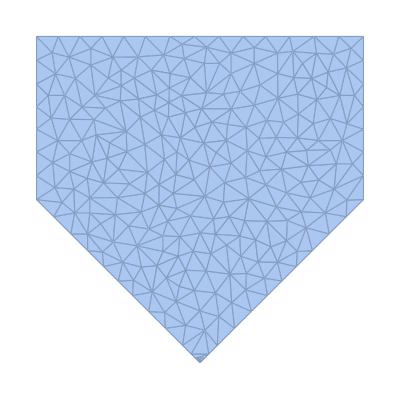

```mathematica
DiscretizeRegion[ImplicitRegion[y>= Abs[x - 1] && y <= 2 && 0<=x<=2, {{x,0,2},{y,-1,2}}], MaxCellMeasure->0.01]
```

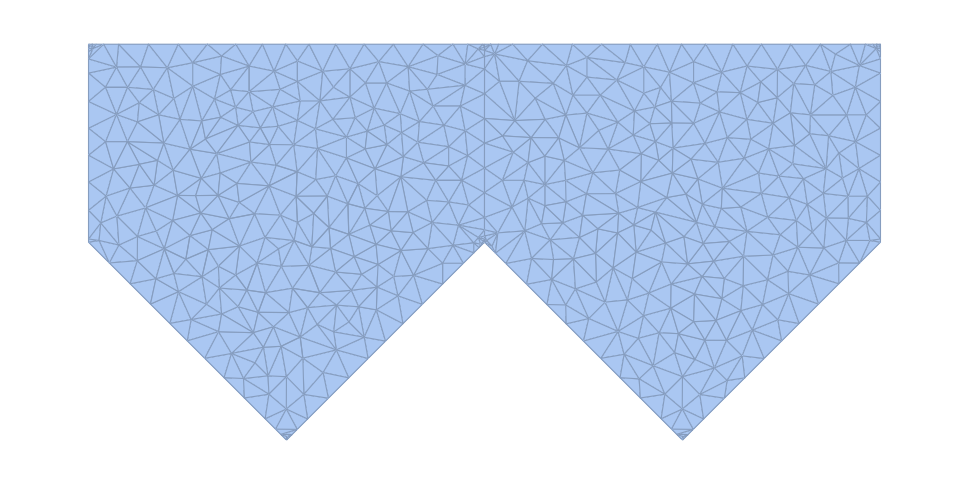

```mathematica
DiscretizeRegion[ImplicitRegion[y>= Piecewise[{{ Abs[x - 1],x<2},{ Abs[x - 3],x>=2}}]  && y <= 2 && 0<=x<=4, {{x,0,4},{y,-1,2}}], MaxCellMeasure->0.01]
```

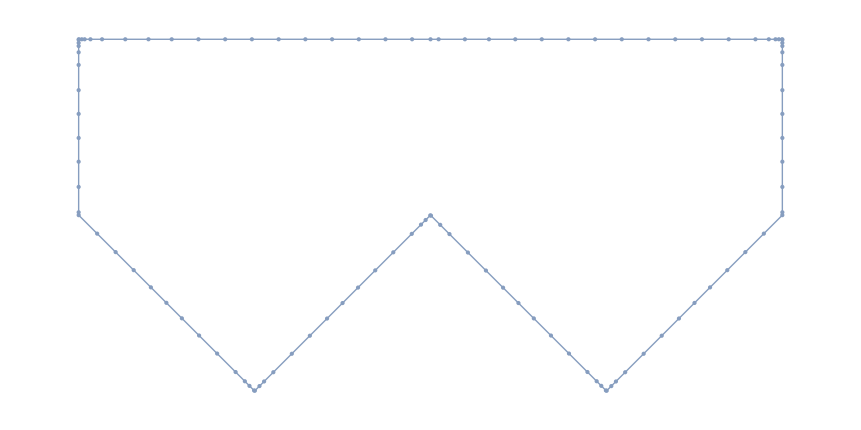

```mathematica
regBound=RegionBoundary[DiscretizeRegion[ImplicitRegion[y>= Piecewise[{{ Abs[x - 1],x<2},{ Abs[x - 3],x>=2}}]  && y <= 2 && 0<=x<=4, {{x,0,4},{y,-1,2}}], MaxCellMeasure->0.01]]
```